#### BC_PlotElasticMaps_gupta.nb Generate Figure 1 of Gupta et al. GJI paper INSTRUCTIONS: Run common_funs, ChooseTmat

```mathematica
Tmat=TmatBrownAn00;
```

```mathematica
PrintFigures=False;
```

```mathematica
plotpoints=30;
```

```mathematica
Kmat[Σ_]:=Closest[Tmat,Σ]
Umat[Σ_]:=UT[Tmat,Σ]
```

```mathematica
Tmat==Transpose[Tmat]
If[!(Tmat==Transpose[Tmat]),MatrixForm[Tmat-Transpose[Tmat]]]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

T is BrownAn00

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

#### output for printing figures

```mathematica
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
otag=FileNameJoin[{odir,"PlotElasticMaps_"<>Tlab[Tmat]}]
```

/Users/carltape/mma/elasticity

/Users/carltape/mma/elasticity/pdf_print

/Users/carltape/mma/elasticity/pdf_print/PlotElasticMaps_BrownAn00

#### Check some settings; don’t set ShiftToEye to zero (see chooseTmat.nb)

```mathematica
AngRadDisk
ShiftToEye
eye
tknsForGC
hueGreen
ColorData["TemperatureMap"][0]
ColorData["TemperatureMap"][.05]
```

0.0349066

0.04

{25 √3 Cos[25 °],25 Cos[25 °],50 Sin[25 °]}

0.008

Hue[0.4, 1, 0.8]

RGBColor[0.178927, 0.305394, 0.933501]

RGBColor[0.2568184, 0.3872628, 0.9379368]

#### example alpha sphere (options defined in ChooseTmat.nb)

```mathematica
Show[cpMONO[Kmat[ORTH],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],{options}]
```

-Graphics3D-

#### legend

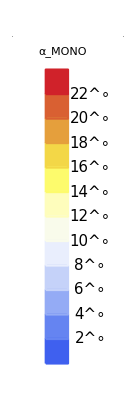

```mathematica
lincrement=1;loffset=2.0;lfontsize=15;lhw=1.1;
plegendx=legends[contours[Tmat,MONO],MaxForScaling[Tmat,MONO],SubscriptBox[Style["α",28],Style["MONO",10]]//DisplayForm,lhw,lfontsize,lincrement,loffset]
```

#### kludge to ensure that the spheres are plotted the same size as each other

```mathematica
Ubasepts[Σ_]:=Flatten[{#,-#}&/@Transpose[Umat[Σ]],1]
Uextrapts[Σ_]:=1.04 lengthAxis Join[Ubasepts[Σ],{{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}}];
```

```mathematica
Uextrapts[Σ]
```

{{-0.336542,-0.962726,-0.964943},{0.336542,0.962726,0.964943},{-1.35837,0.154455,0.319659},{1.35837,-0.154455,-0.319659},{-0.113037,1.01021,-0.968463},{0.113037,-1.01021,0.968463},{1.404,0.,0.},{-1.404,0.,0.},{0.,1.404,0.},{0.,-1.404,0.},{0.,0.,1.404},{0.,0.,-1.404}}

#### settings for axis arrows

```mathematica
lengthAxis= 1.35;
BBrad=1;
ArrowScale=0.17;
tkns=0.009;
```

#### various functions for plotting axis arrows

```mathematica
PaxesForLattice={Paxes[True,True,True,id,{0,0,0},lengthAxis,BBrad,ArrowScale,tkns,"Gray",ArrowColor],{PointSize[ptsz],Point/@extrapts}};
```

```mathematica
PaxesForLatticeU[Σ_,a1_,a2_,a3_]:={Paxes[a1,a2,a3,Umat[Σ],{0,0,0},lengthAxis,BBrad,ArrowScale,tkns,"TriColor",ArrowColor],{PointSize[ptsz],Point/@Uextrapts[Σ]}};
```

#### plotting spheres with arrows

```mathematica
isize=330;
```

```mathematica
pSig[Σ_]:=Show[{cpMONO[Kmat[Σ],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,PaxesForLatticeU[Σ,True,True,True],AllFoldGraphics[Σ,Umat[Σ],ShiftToEye,eye]}]},options,ImageSize->isize];
```

```mathematica
p1=Show[{cpMONO[Tmat,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],
Graphics3D[{PaxesForLattice,PaxesForLatticeU[MONO,True,True,True],AllFoldGraphics[MONO,Umat[MONO],ShiftToEye,eye]}]},options,
ImageSize->isize];
p2=pSig[MONO];
p3=pSig[ORTH];
plegend=Show[plegendx,ImageSize->100];
pall=GraphicsRow[{p1,p2,p3,plegend},ImageSize->1000,Spacings->-10];
```

```mathematica
ofile=otag<>"_alphasphere.pdf";
If[PrintFigures,Export[ofile,pall],pall]
```

/Users/carltape/mma/elasticity/pdf_print/PlotElasticMaps_BrownAn00_alphasphere.pdf

```mathematica
(*Show[{cpMONO[Tmat,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],Graphics3D[PaxesForLattice]},options,ImageSize->800]*)
```

```mathematica
fsz = 18;
p1Labeled=Graphics[{Inset[p1],Text[Style["(a)",fsz,Bold],Scaled[{0.1,0.9}]]}];
p2Labeled=Graphics[{Inset[p2],Text[Style["(b)",fsz,Bold],Scaled[{0.1,0.9}]]}];
p3Labeled=Graphics[{Inset[p3],Text[Style["(c)",fsz,Bold],Scaled[{0.1,0.9}]]}];
pallLabeled=GraphicsRow[{p1Labeled,p2Labeled,p3Labeled,plegend},ImageSize->1000,Spacings->-10];
ofile=otag<>"_alphasphere_labs.pdf";
If[PrintFigures,Export[ofile,pallLabeled],pallLabeled]
```

/Users/carltape/mma/elasticity/pdf_print/PlotElasticMaps_BrownAn00_alphasphere_labs.pdf

#### change the viewpoint such that u3 is pointing toward the viewer, u2 is pointing to the top of the page, u1 to the right

```mathematica
eyeX[Tmat_,Σ_,eyerad_]:=eyerad UT[Tmat,Σ].{0,0,1};
vertX[Tmat_,Σ_]:=UT[Tmat,Σ].{0,1,0};
optionsXnoBox[Tmat_,Σ_,eyerad_]:={ViewPoint->eyeX[Tmat,Σ,eyerad],ViewVertical->vertX[Tmat,Σ],Lighting->{{"Ambient",White}}};
optionsX[Tmat_,Σ_,eyerad_]:={ViewPoint->eyeX[Tmat,Σ,eyerad],ViewVertical->vertX[Tmat,Σ],Lighting->{{"Ambient",White}},Boxed->False};
```

```mathematica
Σ=MONO;
eyerad=50;
```

#### ensure that the two boxes are congruent and that the colored arrows are correctly aligned

```mathematica
Print["Σ = ",Σ];
Print["eyeX = ",eyeX[Tmat,Σ,eyerad]];
Print["vertX = ",vertX[Tmat,Σ]];
Print["Umat[Σ] = ",MatrixForm[Umat[Σ]]];
Print["optionsX[Tmat,MONO,eyerad] = ",optionsX[Tmat,MONO,eyerad]];
Show[{(*cpMONO[Tmat,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],*)
Graphics3D[{PaxesForLattice,PaxesForLatticeU[Σ,True,True,True],
{PointSize[ptsz],Point/@Uextrapts[Σ]}}]},optionsXnoBox[Tmat,MONO,eyerad],Boxed->True,ImageSize->isize]
Show[{(*cpMONO[Tmat,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],*)
Graphics3D[{                                      PaxesForLatticeU[Σ,True,True,True],
{PointSize[ptsz],Point/@Uextrapts[Σ]}}]},optionsXnoBox[Tmat,MONO,eyerad],Boxed->True,ImageSize->isize]
```

Σ = MONO

eyeX = {-4.02552,35.976,-34.4894}

vertX = {-0.967502,0.110011,0.227677}

Umat[Σ] = (-0.239703 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)

optionsX[Tmat,MONO,eyerad] = {ViewPoint→{-4.02552,35.976,-34.4894},ViewVertical→{-0.967502,0.110011,0.227677},Lighting→{{Ambient,GrayLevel[1]}},Boxed→False}

-Graphics3D-

-Graphics3D-

```mathematica
p1top=Show[{cpMONO[Tmat,contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLatticeU[Σ,True,True,False]}]},optionsX[Tmat,MONO,eyerad],ImageSize->isize];

p2top=Show[{cpMONO[Kmat[Σ],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLatticeU[Σ,True,True,False]}]},optionsX[Tmat,MONO,eyerad],ImageSize->isize];
```

```mathematica
Σ=ORTH;
p3top=Show[{cpMONO[Kmat[Σ],contours[Tmat,MONO],MaxForScaling[Tmat,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLatticeU[Σ,True,True,False]}]},optionsX[Tmat,Σ,eyerad],ImageSize->isize];
```

```mathematica
palltop=GraphicsRow[{p1top,p2top,p3top,plegend},ImageSize->1000,Spacings->-10];
```

```mathematica
ofile=otag<>"_alphasphere_top.pdf";
If[PrintFigures,Export[ofile,palltop],palltop]
```

/Users/carltape/mma/elasticity/pdf_print/PlotElasticMaps_BrownAn00_alphasphere_top.pdf

```mathematica
p1Labeled=Graphics[{Inset[p1top],Text[Style["(d)",fsz,Bold],Scaled[{0.1,0.9}]]}];
p2Labeled=Graphics[{Inset[p2top],Text[Style["(e)",fsz,Bold],Scaled[{0.1,0.9}]]}];
p3Labeled=Graphics[{Inset[p3top],Text[Style["(f)",fsz,Bold],Scaled[{0.1,0.9}]]}];
palltopLabeled=GraphicsRow[{p1Labeled,p2Labeled,p3Labeled,plegend},ImageSize->1000,Spacings->-10];
```

```mathematica
ofile=otag<>"_alphasphere_labs_top.pdf";
If[PrintFigures,Export[ofile,palltopLabeled],palltopLabeled]
```

/Users/carltape/mma/elasticity/pdf_print/PlotElasticMaps_BrownAn00_alphasphere_labs_top.pdf